# Transfer function of string (Problem 3.18)

```mathematica
Clear["Global`*"];
```

```mathematica
(* Manipulate[
Plot[{Abs[Sin[π ω(1-x)]/Sin[π ω]],1-x},{ω,0,10},PlotStyle->{,Directive[Gray,Dashed,Thin]},PlotRange->{0,5}],{{x,0.5},0,1}] *)
```

special cases

```mathematica
{tf1,tf2,tf3}=Sin[π ω(1-x)]/Sin[π ω]/.x->{1/2,1/4,3/4}//Simplify
```

{1/2 Sec[(π ω)/2],Csc[π ω] Sin[(3 π ω)/4],Csc[π ω] Sin[(π ω)/4]}

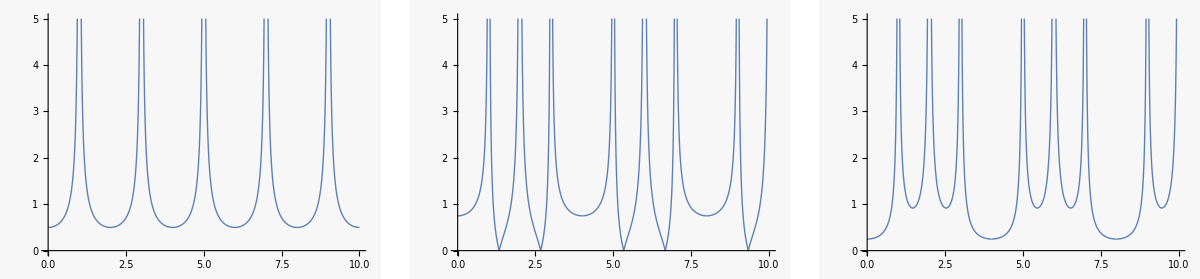

```mathematica
p1=Plot[Abs[tf1],{ω,0,10},PlotRange->{0,5}];
p2=Plot[Abs[tf2],{ω,0,10},PlotRange->{0,5}];
p3=Plot[Abs[tf3],{ω,0,10},PlotRange->{0,5}];
GraphicsRow[{p1,p2,p3}]
```

For free end at L,  Sin → Cos

```mathematica
Manipulate[
Plot[{Abs[Cos[π ω(1-x)]/Cos[π ω]],1},{ω,0,5},PlotStyle->{,Directive[Gray,Dashed,Thin]},PlotRange->{0,5}],{{x,0.5},0,1}]
```

```mathematica
{tf4,tf5,tf6}=Cos[π ω(1-x)]/Cos[π ω]/.x->{1/4,1/2,1}
```

{Cos[(3 π ω)/4] Sec[π ω],Cos[(π ω)/2] Sec[π ω],Sec[π ω]}

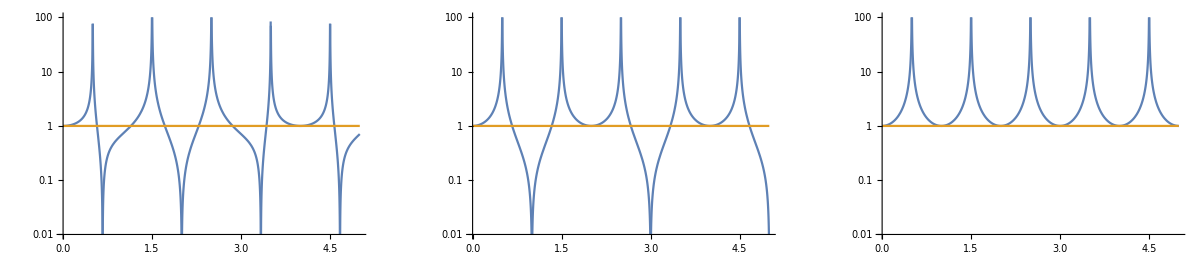

```mathematica
p4=LogPlot[{Abs[tf4],1},{ω,0,5},PlotRange->{0.01,100}];
p5=LogPlot[{Abs[tf5],1},{ω,0,5},PlotRange->{0.01,100}];
p6=LogPlot[{Abs[tf6],1},{ω,0,5},PlotRange->{0.01,100}];
GraphicsRow[{p4,p5,p6}]
```

```mathematica
dg=D[Cos[π ω(1-x)]/Cos[π ω]/.x->1/4,ω]//Simplify
```

1/8 π Sec[π ω]^2 (7 Sin[(π ω)/4]+Sin[(7 π ω)/4])

Brief look at the time domain.

```mathematica
eq=D[ψ[x,t], x,x]==D[ψ[x,t], t,t];
init=ψ[x,0]==0;
bc0=ψ[0,t]==Sin[2π t];
bc1=ψ[1,t]==0;  
ψsol=NDSolveValue[{eq,init,bc0,bc1},ψ,{x,0,1},{t,0,10}];
Plot3D[ψsol[x,t],{x,0,1},{t,0,10}, PlotRange->All]
```

-Graphics3D-